#### Data

```mathematica
Clear["Global`*"]
(*units and constants for trap depth mostly*)
kHz=10^3;
nm=10^-9;
mK=10^-3;
uK=10^-6;
us=10^-6;
kB=1.38064852 10^-23;
ℏ=1.0545718 10^-34;
amu=1.66054 10^-27;
λtrap=976 nm;
m=132.90545 amu;23amu;
Needs["ErrorBarLogPlots`"];
SetDirectory[NotebookDirectory[]];

params=Import["params.csv"][[1]];
survNonInt=Transpose[Import["surv.csv"]][[;;,4]]; 
survInt=Transpose[Import["surv.csv"]][[;;,2]]; 

survNonIntErr=Transpose[Import["survErr.csv"]][[;;,4]];
survIntErr=Transpose[Import["survErr.csv"]][[;;,2]];

(*only take the first half.. what are the 2 halves??*)

i=1;
len=61;
dataNonInt=Thread[{Thread[{-50+3(params-((i-1)len+1)) ,survNonInt}],ErrorBar[#]&/@survNonIntErr}][[(i-1)len +1;;i len]];
dataInt=Thread[{Thread[{-50+3(params-((i-1)len+1)) ,survInt}],ErrorBar[#]&/@survIntErr}][[(i-1)len +1;;i len ]];
```

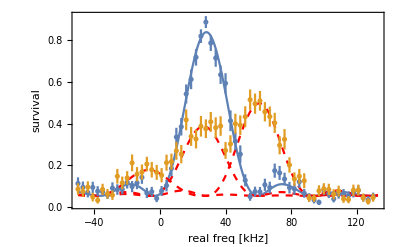

{W→11.5732,f0→28.3088}

{W1→6.53485,W2→-7.74009,W3→3.81839,f01→26.6019,f02→60.5357,f03→-7.06085}

```mathematica
Clear[t];
Pe[f_,f0_,W_,t_]:= ( W)^2/((W)^2+(f-f0)^2)Sin[ t π √(W^2+(f-f0)^2)]^2;   (*in real frequency*) 
t=30 10^-3;
offs=.0523;
nlmNonInt=NonlinearModelFit[dataNonInt[[;;,1]],Pe[f,f0,W,t]+offs,{{W,10},{f0,28}},f];
nlmInt=NonlinearModelFit[dataInt[[;;,1]],
 Pe[f,f01,W1,t]+
Pe[f,f02,W2,t]+
Pe[f,f03,W3,t]+
offs,{{W1,10},{W2,10},{W3,10},{f01,58},{f02,-4},{f03,-20}},f];

Show[{Plot[{nlmNonInt[f],
(*nlmInt[f]*)},{f,-50,133},PlotRange->All,
Axes->False,Frame->True,FrameLabel->{"real freq [kHz]","survival","i="<>ToString[i]},LabelStyle->{Black,17
}]
,
Plot[{
Pe[f,f01,W1,t]+offs/.nlmInt["BestFitParameters"],
Pe[f,f02,W2,t]+offs/.nlmInt["BestFitParameters"],
Pe[f,f03,W3,t]+offs/.nlmInt["BestFitParameters"]},{f,-50,133},PlotRange->All,PlotStyle->{{Red,Dashed}}],

ErrorListPlot[{dataNonInt,dataInt}]}]
nlmNonInt["BestFitParameters"]
nlmInt["BestFitParameters"]
```

# expected shift:-13(7)kHz does a nearby molecular state cause shift??? unklikely that Cs is that hot... try w Na temp distribution (but that still wont change the sign of the shift. check rabi flopping.